```mathematica
β[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=
β[ω,δ,t,ϵ1,ϵ2,m]=ReplacePart[ReplacePart[ReplacePart[0*IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->t],Table[{a,a},{a,1,2m,2}]->ω+ⅈ*δ-ϵ1],Table[{b,b},{b,2,2m,2}]->ω+ⅈ*δ-ϵ2]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
leads= Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/hBN/leads/lead_right_1_0.75_hbn_"<>ToString[ω]<>".dat"]],{ω,Range[-3.5,3.5,0.01]}]
```

{{{-0.271682-0.0000102439 ⅈ,16,-0.111365-9.4929×10^-6 ⅈ},16,{1}},699,{1}}
 |  |  |  |

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=LEFT[ω,δ,t,ϵ1,ϵ2,m]=(*leads[[Round[ω*100+351]]]*)Module[{J=Inverse[β[ω,δ,t,ϵ1,ϵ2,m]],B:=Inverse[β[ω,δ,t,ϵ1,ϵ2,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,20000]; J=J]
```

```mathematica
LEFT1[ω_,δ_,t_,ϵ1_,ϵ2_,m_,X_]:=(*leads[[Round[ω*100+351]]]*)Module[{J=Inverse[β[ω,δ,t,ϵ1,ϵ2,m]],B:=Inverse[β[ω,δ,t,ϵ1,ϵ2,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,X]; J=J]
```

```mathematica
Monitor[Table[Abs[LEFT1[x,0.0001,1,1,-0.5,9,20000][[1,1]]-LEFT1[x,0.0001,1,1,-0.5,9,20000+10][[1,1]]],{x,0,3,0.01}],x]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.71051×10^-20,2.71051×10^-20,2.71051×10^-20,5.42101×10^-20,0.,5.42101×10^-20,0.,1.0842×10^-19,2.22045×10^-16,5.42101×10^-20,2.22045×10^-16,2.22045×10^-16,1.6263×10^-19,5.20417×10^-18,0.000692891,0.00382336,0.00827393,0.0135198,0.0195063,0.0288769,0.0305062,0.0356773,0.0490599,0.0355386,0.0399182,0.0797245,0.0583707,0.00783285,0.0610391,0.177406,0.178939,0.173417,0.0238169,0.300042,0.24295,0.241845,0.386931,0.0943089,0.0553275,0.0159082,0.329099,0.105335,0.0317439,0.0606902,0.23805,0.587835,0.219959,0.462035,0.197991,0.46463,0.460095,0.256474,0.107801,0.304289,0.584778,0.648497,0.533524,0.213127,0.317187,0.408932,0.424465,0.320875,0.569714,0.594292,0.481754,0.363712,0.666481,0.469745,0.325844,0.474589,0.540954,0.832014,0.492945,0.756904,0.456599,0.321281,0.0848122,0.617149,0.364943,0.639403,0.679551,0.91064,0.247491,0.667322,0.451259,0.431321,0.203477,0.245284,0.720259,0.599332,0.498145,0.621664,0.1913,0.191333,0.564124,0.377894,0.180436,0.563482,0.50648,0.315578,0.330535,0.6016,0.171224,0.330786,0.253147,0.305299,0.4838,0.459588,0.453717,0.711377,0.361926,0.212829,0.49227,0.395689,0.429241,0.139927,0.108817,0.366889,0.400521,0.310861,0.370162,0.378356,0.370776,0.285365,0.34891,0.295273,0.154132,0.486127,0.256776,0.395169,0.580061,0.342046,0.0550237,0.356255,0.477394,0.456426,0.253301,0.332554,0.338632,0.319647,0.29587,0.241534,0.319795,0.360957,0.449389,0.278145,0.36113,0.236254,0.196569,0.0535651,0.196991,0.301548,0.147126,0.0431949,0.272414,0.077045,0.210049,0.215101,0.0818274,0.167221,0.313926,0.129406,0.143992,0.144571,0.137665,0.0541922,0.136982,0.213732,0.137846,0.0706365,0.133136,0.136293,0.155575,0.0606825,0.0783156,0.0955776,0.130073,0.100877,0.156432,0.139916,0.119575,0.0507271,0.14709,0.160169,0.0633147,0.112651,0.11786,0.077184,0.136173,0.0558928,0.100934,0.0173045,0.0568487,0.079589,0.0495546,0.0113046,0.0678715,0.0555164,0.0645183,0.0519287,0.0457973,0.0448004,0.0469491,0.0398161,0.0246018,0.0371149,0.0246646,0.0230341,0.0245984,0.0246167,0.0238458,0.0227774}

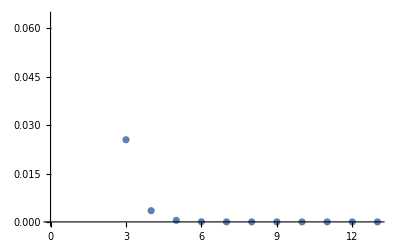

```mathematica
ListPlot[%125]
```

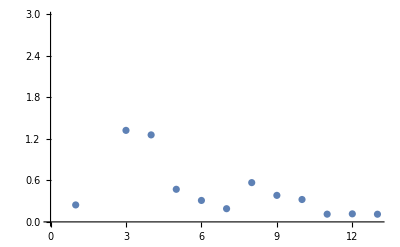

```mathematica
ListPlot[%123]
```

```mathematica
Monitor[Table[{ω,-Im[LEFT1[ω,0.00001,1,1,-0.5,9,10][[1,1]]]},{ω,Range[0,3,0.01]}],ω]//ListLinePlot
```

```mathematica
Monitor[Table[{ω,-Im[LEFT[ω,0.00011,,1,-0.5,9][[3,3]]]},{ω,Range[0,3,0.01]}],ω]//ListLinePlot
```

Part::partd: Part specification LEFT[0.,0.00001,1,-0.5,9]⟦3,3⟧ is longer than depth of object.

Part::partd: Part specification LEFT[0.01,0.00001,1,-0.5,9]⟦3,3⟧ is longer than depth of object.

Part::partd: Part specification LEFT[0.02,0.00001,1,-0.5,9]⟦3,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

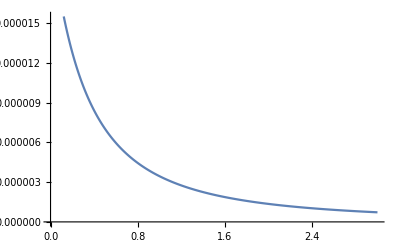

```mathematica
ListPlot[%110,Joined->True]
```

```mathematica
g[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= Inverse[β[ω,δ,t,ϵ1,ϵ2,m]]
SR[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ1,ϵ2,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ1,ϵ2,m].T1[t,m]].g[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=SR[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m].SL[ω,δ,t,ϵ2,ϵ1,m].ConjugateTranspose[ρ[t,m]]].SL[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ2,ϵ1,m].ρ[t,m].SL[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m]].SL[ω,δ,t,ϵ2,ϵ1,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= IL[ω,δ,t,ϵ1,ϵ2,m]-ConjugateTranspose[IL[ω,δ,t,ϵ1,ϵ2,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= IR[ω,δ,t,ϵ1,ϵ2,m]-ConjugateTranspose[IR[ω,δ,t,ϵ1,ϵ2,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= SL[ω,δ,t,ϵ2,ϵ1,m].ρ[t,m].IL[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= Gnonlocal[ω,δ,t,ϵ1,ϵ2,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ1,ϵ2,m]]
```

```mathematica
pris[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m].grr[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m].GNON[ω,δ,t,ϵ1,ϵ2,m]]]
```

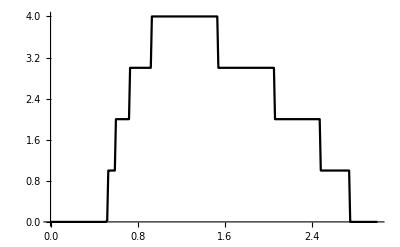

```mathematica
ListLinePlot[Monitor[Table[{ω,pris[ω,0.0001,1,-1,0.5,9]},{ω,Range[0,3,0.01]}],ω],PlotStyle->Black]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist,list]
```

```mathematica
list[total_,num_]:=Transpose[Join[{Range[1,100]},{RandomSample[Join[Table[0,100-total],Flatten[Join[Table[RandomSample[Range[1,18,2],1],total-num],Table[RandomSample[Range[2,18,2],1],num]]]]]}]]
```

```mathematica
dist[total_,num_]:=dist[total,num]=Table[list[total,num],5000]
```

```mathematica
dist[50,25][[1]]
```

{{1,2},{2,0},{3,6},{4,0},{5,8},{6,9},{7,0},{8,7},{9,0},{10,0},{11,0},{12,15},{13,0},{14,4},{15,9},{16,0},{17,0},{18,6},{19,0},{20,8},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,9},{28,0},{29,0},{30,0},{31,8},{32,5},{33,14},{34,0},{35,0},{36,3},{37,0},{38,6},{39,0},{40,18},{41,0},{42,0},{43,0},{44,0},{45,13},{46,0},{47,4},{48,2},{49,0},{50,10},{51,11},{52,11},{53,12},{54,10},{55,0},{56,16},{57,5},{58,15},{59,5},{60,8},{61,5},{62,5},{63,0},{64,11},{65,0},{66,15},{67,14},{68,0},{69,0},{70,11},{71,0},{72,2},{73,10},{74,10},{75,0},{76,16},{77,0},{78,18},{79,0},{80,11},{81,0},{82,0},{83,0},{84,0},{85,9},{86,0},{87,0},{88,0},{89,0},{90,0},{91,5},{92,18},{93,1},{94,9},{95,5},{96,0},{97,1},{98,0},{99,0},{100,10}}

```mathematica
device[ω_,δ_,t_,ϵ_,m_,total_,number_,conc_]:=Module[{abc=dist[total,conc][[number]],Z={}},
sl1= Module[{J1=SL[ω,δ,t,-1,0.5,m]},Do[
J1=Inverse[IdentityMatrix[2m]-Inverse[Module[{J=β[ω,δ,t,-1,0.5,9],xx= dist[total,conc][[number]][[unitcell,2]]},ReplacePart[J,{{xx,xx}}->ω+ⅈ*δ-ϵ]]].ConjugateTranspose[T1[t,m]].J1.T1[t,m]].Inverse[Module[{J=β[ω,δ,t,-1,0.5,9],xx= dist[total,conc][[number]][[unitcell,2]]},ReplacePart[J,{{xx,xx}}->ω+ⅈ*δ-ϵ]]],{unitcell,100}];{J1,Z}];
il1:=Inverse[IdentityMatrix[2m]-sl1[[1]].ρ[1,m].SL[ω,δ,t,0.5,-1,m].ConjugateTranspose[ρ[1,m]]].sl1[[1]];
ir1:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,0.5,-1,m].ρ[1,m].sl1[[1]].ρ[1,m]].SL[ω,δ,t,0.5,-1,m];gdd1:=il1-ConjugateTranspose[il1];grr1:= ir1-ConjugateTranspose[ir1];Gnonlocal1:= SL[ω,δ,t,0.5,-1,m].ρ[1,m].il1;GNON1:=Gnonlocal1-ConjugateTranspose[Gnonlocal1];tr1=Abs[Tr[gdd1.ρ[1,m].grr1.ρ[1,m]-ρ[1,m].GNON1.ρ[1,m].GNON1]];If[tr1>pris[ω,0.0001,1,-1,0.5,9],pris[ω,0.0001,1,-1,0.5,9],tr1]]
```

```mathematica
Table[{w,Mean[ParallelTable[device[w,0.0001,1,0,9,70,num,35],{num,1000}]]},{w,Range[1,3,0.01]}]
```

{56.3143,0.776974}

```mathematica
Monitor[Table[Mean[ParallelTable[device[2,0.0001,1,0,9,70,num,x],{num,200}]],{x,15,55,5}],x]
```

{0.393693,0.40592,0.342855,0.388238,0.374337,0.425579,0.413101,0.406493,0.402379}

```mathematica
Mean[ParallelTable[device[1,0.0001,1,0,9,70,num,35],{num,2500}]]//AbsoluteTiming
```

{56.4542,0.772839}

```mathematica
0.776489
```

```mathematica
dist[10,5][[1]]
```

{{1,0},{2,0},{3,0},{4,0},{5,6},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,7},{17,8},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,17},{31,10},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,3},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,1},{54,0},{55,0},{56,0},{57,0},{58,0},{59,12},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0},{67,0},{68,0},{69,0},{70,3},{71,0},{72,0},{73,0},{74,0},{75,0},{76,0},{77,0},{78,0},{79,0},{80,0},{81,0},{82,0},{83,0},{84,0},{85,0},{86,0},{87,0},{88,0},{89,0},{90,0},{91,0},{92,0},{93,0},{94,0},{95,0},{96,0},{97,6},{98,0},{99,0},{100,0}}

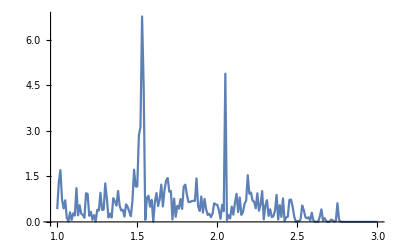

```mathematica
ListLinePlot[ParallelTable[{ω,device[ω,0.0001,1,0,9,70,1,35]},{ω,Range[1,3,0.01]}],PlotRange->All]
```

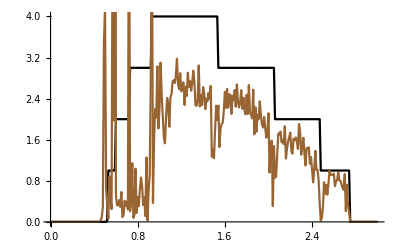

```mathematica
Show[%35,ListLinePlot[ParallelTable[{ω,device[ω,0.0001,1,0,9,10,1,7]},{ω,Range[0,3,0.01]}],PlotStyle->Brown]]
```

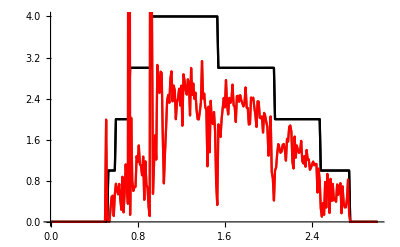

```mathematica
Show[%82,%79]
```

```mathematica
Monitor[Table[Monitor[Table[Export["/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_"<>ToString[total]<>"_"<>ToString[x]<>"_N_boron.dat",Table[{ω,Mean[ParallelTable[device[ω,0.0001,1,0,9,total,num,x],{num,500}]]},{ω,Range[0,3,0.01]}]],{x,5,total,5}],x],{total,80,100,10}],total]
```

{{/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_40_5_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_40_10_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_40_15_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_40_20_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_40_25_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_40_30_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_40_35_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_40_40_N_boron.dat},{/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_50_5_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_50_10_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_50_15_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_50_20_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_50_25_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_50_30_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_50_35_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_50_40_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_50_45_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_50_50_N_boron.dat},{/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_60_5_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_60_10_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_60_15_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_60_20_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_60_25_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_60_30_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_60_35_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_60_40_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_60_45_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_60_50_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_60_55_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_60_60_N_boron.dat},{/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_5_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_10_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_15_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_20_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_25_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_30_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_35_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_40_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_45_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_50_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_55_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_60_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_65_N_boron.dat,/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_70_70_N_boron.dat}}

```mathematica
device[1,0.001,1,0,9,50,11,30]
```

1.45023

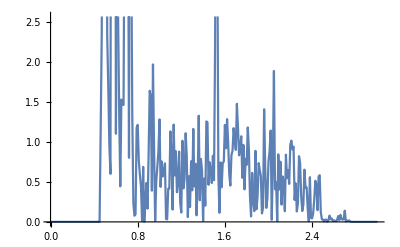
{39.2728,-Graphics-}

```mathematica
ListLinePlot[ParallelTable[{ω,device[ω,0.0001,1,0,9,70,2,45]},{ω,Range[0,3,0.01]}]]//AbsoluteTiming
```

```mathematica
Last[%152]
```

-Graphics-

```mathematica
input=Table[ParallelTable[{ω,device[ω,0.0001,1,0,9,50,num,20]},{ω,Range[0,3,0.01]}],{num,10}]
```

{{{0.,4.74589×10^-8},{0.01,4.8227×10^-8},{0.02,4.90463×10^-8},{0.03,4.99201×10^-8},{0.04,5.0852×10^-8},292,{2.97,5.117×10^-8},{2.98,4.70796×10^-8},{2.99,4.3452×10^-8},{3.,4.02226×10^-8}},8,{1}}
 |  |  |  |

```mathematica
a[x_]:= Table[b,{b,Range[5,x,1]}]
```

```mathematica
a[10]
```

{5,6,7,8,9,10}

```mathematica
transmission[total_]:=transmission[total]= Table[Import["/home/shardulmukim/PhD/fwi/hBN/CA/hBN_CA_"<>ToString[total]<>"_"<>ToString[x]<>"_N_boron.dat"],{x,Range[5,total,5]}]
```

```mathematica
Clear[transmission]
```

```mathematica
misfit[n_,x_,y_]:=Table[{total,Module[{m5=input[[n]]},
ρ1:= Table[Module[{B1=Transpose[{m5[[1;;301]][[;;,1]],(m5[[1;;301,2]]-transmission[total][[ξ]][[1;;301,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{ξ,Dimensions[transmission[total]][[1]]}]; 
a1=Transpose[Join[{Range[5,total,5]},{ρ1}]];{a1[[Position[a1,Min[a1]][[1,1]]]]}]},{total,Range[40,100,10]}]
```

```mathematica
misfitl[total_,n_,x_,y_]:=Module[{m5=input[[n]]},
ρ1:=ParallelTable[Log[Module[{B1=Transpose[{m5[[1;;301]][[;;,1]],(m5[[1;;301,2]]-transmission[total][[ξ]][[1;;301,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]]^5,{ξ,Dimensions[transmission[total]][[1]]}]; 
a1=Transpose[Join[{total*Array[f123,Dimensions[transmission[total]][[1]]]},{Range[5,total,5]},{ρ1}]];{a1,a1[[Position[a1,Min[a1]][[1,1]]]]}]
```

```mathematica
f123[x_]:=x/x
```

```mathematica
a[n_,x_,y_]:=misfit[n,x,y][[Position[misfit[n,x,y],Min[misfit[n,x,y]]][[1,1]]]]
```

```mathematica
SortBy[Module[{J=misfitl[40,1,1.45,0.95][[1]]},Do[J=Join[misfitl[total,1,1.45,0.95][[1]],J],{total,50,100,10}];J],First]
```

```mathematica
Show[ListContourPlot[%1,PlotRange->{{40,100},{5,40}},ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}],PlotLegends->Placed[Automatic,Right],FrameLabel->{{HoldForm[Subscript[N, B]],None},{HoldForm[Subscript[N, N]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",20,GrayLevel[0]}],ListLinePlot[Join[{Table[{x,20},{x,40,100}],Table[{50,x},{x,5,50}]}],PlotStyle->{Directive[Dashed,Red]}]]
```

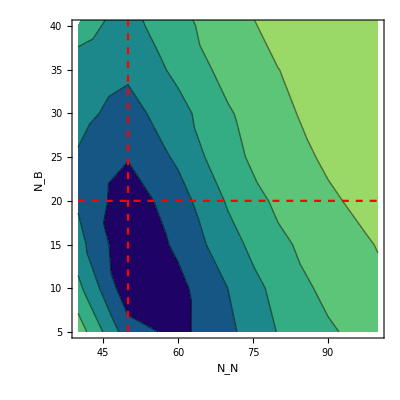
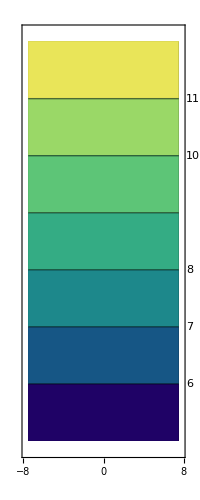

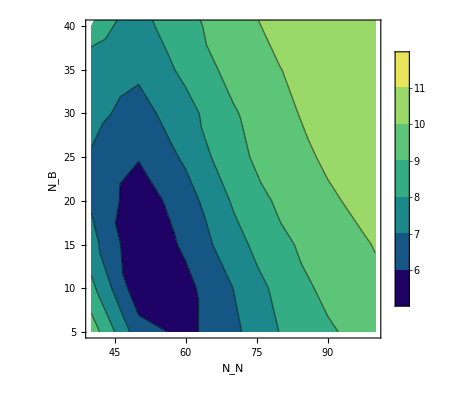

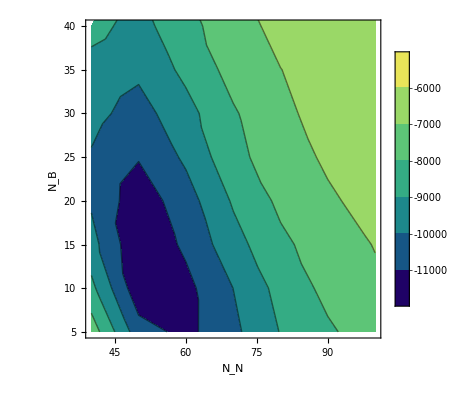

```mathematica
%19[[2]]
```

Placed[,Right,Identity]

```mathematica
Show[%15,ListLinePlot[Join[{Table[{x,20},{x,40,100}],Table[{50,x},{x,5,50}]}],PlotStyle->{Directive[Dashed,Red]}]]
```

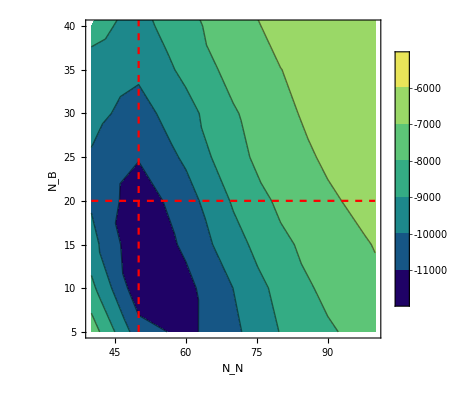

-Graphics-

```mathematica
Export["~/PhD/hbn_sur.pdf",%17]
```

~/PhD/hbn_sur.pdf

```mathematica
Show[%5,FrameLabel->{{HoldForm[Subscript[N, B]],None},{HoldForm[Subscript[N, N]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

-Graphics-

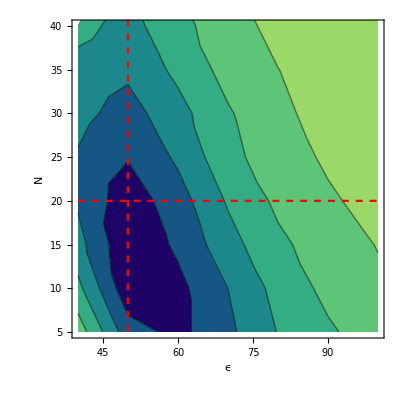

```mathematica
Show[%1,FrameLabel->{{HoldForm[HoldForm[N]],None},{HoldForm[ϵ],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["hbn_sur.pdf",%335]
```

hbn_sur.pdf

```mathematica
Interpolation[%296]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

InterpolatingFunction[…]

```mathematica
MatrixPlot[%279]
```

```mathematica
%279[[Position[%279,Min[%279]][[1,1]]]]
```

{50,15,-3.00208×10^15}

```mathematica
p[total_]:=Transpose[Join[{total*Array[f123,Dimensions[transmission[total]][[1]]]},{Range[5,total,5]}]]
```

```mathematica
Module[{J=p[40]},Do[J=Join[p[total],J],{total,50,100,10}];J]
```

{{95,5},{90,10},{85,15},{80,20},{75,25},{70,30},{65,35},{60,40},{55,45},{50,50},{45,55},{40,60},{35,65},{30,70},{25,75},{20,80},{15,85},{10,90},{5,95},{0,100},{85,5},{80,10},{75,15},{70,20},{65,25},{60,30},{55,35},{50,40},{45,45},{40,50},{35,55},{30,60},{25,65},{20,70},{15,75},{10,80},{5,85},{0,90},{75,5},{70,10},{65,15},{60,20},{55,25},{50,30},{45,35},{40,40},{35,45},{30,50},{25,55},{20,60},{15,65},{10,70},{5,75},{0,80},{65,5},{60,10},{55,15},{50,20},{45,25},{40,30},{35,35},{30,40},{25,45},{20,50},{15,55},{10,60},{5,65},{0,70},{55,5},{50,10},{45,15},{40,20},{35,25},{30,30},{25,35},{20,40},{15,45},{10,50},{5,55},{0,60},{45,5},{40,10},{35,15},{30,20},{25,25},{20,30},{15,35},{10,40},{5,45},{0,50},{35,5},{30,10},{25,15},{20,20},{15,25},{10,30},{5,35},{0,40}}

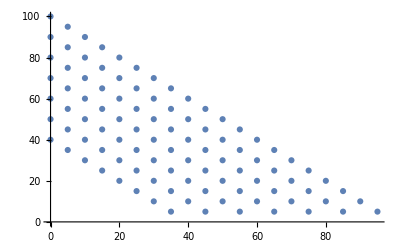

```mathematica
ListPlot[%293]
```

```mathematica
p[total_]:=Table[{total-x,x},{x,Range[5,total,5]}]
```

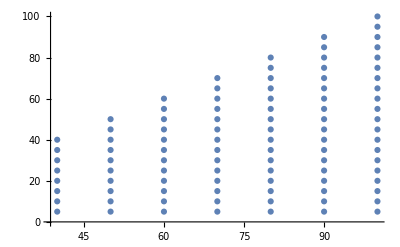

```mathematica
ListPlot[%287]
```

```mathematica
ListPointPlot3D[%279]
```

-Graphics3D-

```mathematica
Interpolation[%279]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

InterpolatingFunction[…]

```mathematica
ListPointPlot3D[%245]
```

-Graphics3D-

```mathematica
Table[misfitl[x,1,2.4,1.5][[1]],{x,40,100,10}]
```

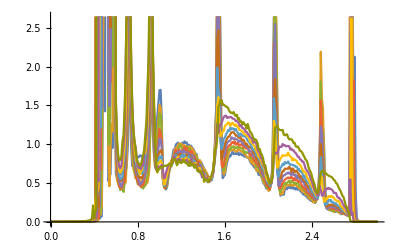

```mathematica
ListLinePlot[transmission[50],PlotRange->]
```

```mathematica
Mean[Abs[Table[Mean[{Flatten[a[n,1.6,2]][[2]],Flatten[a[n,2.1,2.4]][[2]]}],{n,50}]-45]]/45
```

359/900

```mathematica
N[359/900]
```

0.398889

```mathematica
N[259/20]
```

```mathematica
12.95/30
```

0.431667

```mathematica
a[1,1.6,2]//Flatten+a[1,2.1,2.4]//Flatten
```

{50+Flatten,{{30+Flatten,0.000771704+Flatten}}}[{50,{{25,0.00102892}}}]

```mathematica
ListLinePlot[transmission[50]]
```

-Graphics-

```mathematica
misfitl[1,1.1,2.3][[Position[misfitl[1,1.1,2.3],Min[misfitl[1,1.1,2.3]]][[1]]]][[1]][[2]]
```

{{40,0.00165696}}

```mathematica
%83[[1,1]][[1,1]]
```

Part::partd: Part specification 50⟦1,1⟧ is longer than depth of object.

50⟦1,1⟧

```mathematica
Table[misfitl[n,1,2.3][[Position[misfitl[n,1,2.3],Min[misfitl[n,1,2.3]]][[1]]]][[1]][[1]]+misfitl[n,1,2.3][[Position[misfitl[n,1,2.3],Min[misfitl[n,1,2.3]]][[1]]]][[1]][[2]][[1,1]],{n,100}]
```

{90,60,70,115,80,110,110,110,110,70,90,110,90,110,85,80,90,85,90,105,65,110,60,110,60,85,110,85,110,105,135,110,95,110,85,80,110,95,75,90,70,85,80,110,90,70,105,110,85,105,105,110,110,135,110,135,75,110,110,105,95,110,110,90,115,80,85,90,70,115,80,95,80,70,110,90,70,85,110,110,110,70,110,110,110,75,110,90,70,60,110,115,90,110,115,110,110,110,110,85}

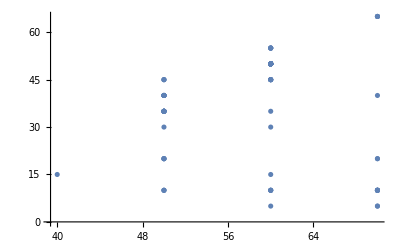

```mathematica
ListPlot[%105]
```

```mathematica
Min[%68]
```

0.0696534

```mathematica
Position[%68,Min[%68]]
```

{{1,2,1,1,2},{1,2,2,2}}

```mathematica
Extract[%68,{{1,2,1,1,2},{1,2,2,2}}]
```

{0.0696534,0.0696534}

```mathematica
misfitr[n_,x_,y_]:=Module[{m5=input[[n]]},
ρ1:= Table[Module[{B1=Transpose[{m5[[1;;601]][[;;,1]],(m5[[1;;601,2]]-transmission[[ξ]][[1;;601,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{ξ,8}]; 
a1=Transpose[Join[{Range[5,40,5]},{ρ1}]];{a1,a1[[Position[a1,Min[a1]][[1,1]]]]}]
```

```mathematica
Abs[Table[misfitl[n,0,-3][[2]][[1]],{n,100}]-20]/20//Mean
```

41/100

```mathematica
ListLinePlot[transmission]
```

```mathematica
gg1[y_]:=Table[{x,y},{x,Range[(y+0.3),3,0.05]}]
```

```mathematica
Clear[ggr,ggl]
```

```mathematica
ggr[n_,y_]:=ggr[n,y]=ParallelTable[misfitl[n,x,y][[2]][[1]],{x,Range[(y+0.3),3,0.02]}]
```

```mathematica
ggl[n_,y_]:=ggl[n,y]=ParallelTable[misfitl[n,x,-3+y][[2]][[1]],{x,Range[(-3+y+0.3),-1,0.02]}]
```

```mathematica
gg1[0.6]
```

gg1[0.6]

```mathematica
r1[r_]:=(N[Mean[Flatten[Table[ggl[r,y],{y,Range[0,1.7,0.02]}]]]]+N[Mean[Flatten[Table[ggr[r,y],{y,Range[0.6,2.7,0.02]}]]]])/2
```

```mathematica
Table[Print[n];r1[n],{n,10}]
```

1

2

3

4

5

6

7

8

9

10

{34.23,35.4016,37.8979,34.7188,33.025,35.388,35.6199,35.4304,33.0585,34.9912}

```mathematica
Mean[%83]
```

2019/124

```mathematica
N[2019/124]
```

16.2823

```mathematica
a[y_]:=Table[{x,y},{x,Range[(y+0.3),3,0.05]}]
```

```mathematica
a[0.5]
```

{{0.8,0.5},{0.85,0.5},{0.9,0.5},{0.95,0.5},{1.,0.5},{1.05,0.5},{1.1,0.5},{1.15,0.5},{1.2,0.5},{1.25,0.5},{1.3,0.5},{1.35,0.5},{1.4,0.5},{1.45,0.5},{1.5,0.5},{1.55,0.5},{1.6,0.5},{1.65,0.5},{1.7,0.5},{1.75,0.5},{1.8,0.5},{1.85,0.5},{1.9,0.5},{1.95,0.5},{2.,0.5},{2.05,0.5},{2.1,0.5},{2.15,0.5},{2.2,0.5},{2.25,0.5},{2.3,0.5},{2.35,0.5},{2.4,0.5},{2.45,0.5},{2.5,0.5},{2.55,0.5},{2.6,0.5},{2.65,0.5},{2.7,0.5},{2.75,0.5},{2.8,0.5},{2.85,0.5},{2.9,0.5},{2.95,0.5},{3.,0.5}}

```mathematica
misfitl[1,-1,-3+0][[1]][[1,2]]
```

0.0165709

```mathematica
fF[n_,y1_,y2_]:=Join[Table[misfitl[n,x,-3+y1][[2]][[1]],{x,Range[(-3+y1+0.3),-1,0.05]}],Table[misfitr[n,x,y2][[2]][[1]],{x,Range[(y2+0.3),3,0.05]}]]
```

```mathematica
Flatten[Table[Table[fF[1,a,y],{a,0,1.5,0.1}],{y,0.5,2.5,0.1}]]
```

{40,40,40,40,40,40,40,40,40,40,40,40,40,40,25,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,40,35,35,35,35,40,40,40,40,40,40,40,25,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,35,35,35,35,35,35,40,40,40,40,25,25,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,14744,25,25,25,25,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,30,30,30,30,30,25,25,15,25,25,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,30,30,30,30,30,15,15,15,15,25,40,40,40,40,40,40,40,40,40,40,40,40,40,40,30,30,30,30,30,5,5,5,10,40,40,40,40,40,40,40,40,40,40,40,40,40,30,30,30,30,30,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,30,30,30,30,30,40,40,40,40,40,40,40,40,40,40,40,40,40,30,30,30,30,30,40,40,40,40,40,40,40,40,40,40,40,30,30,30,30,30,40,40,40,40,40,40,40,40,40,30,30,30,30,30,40,40,40,40,40,40,40,30,30,30,30,30,40,40,40,40,40,30,30,30,30,30}
 |  |  |  |

```mathematica
Mean[%79]
```

296/9

```mathematica
N[296/9]
```

32.8889

```mathematica
fF1[n_,y1_,y2_]:=Join[Table[misfitl[n,x,-3+y1][[1]],{x,Range[(-3+y1+0.3),-1,0.05]}],Table[misfitr[n,x,y2][[1]],{x,Range[(y2+0.3),3,0.05]}]]
```

```mathematica
Mean[fF1[1,0,0.5]]
```

{{5,7.31152},{10,6.44504},{15,13.8654},{20,0.608092},{25,0.225879},{30,0.584274},{35,4.90822},{40,13.1499}}

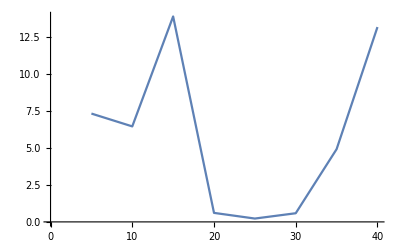

```mathematica
ListPlot[{{5,7.31151756307186},{10,6.445035641779148},{15,13.865356543040136},{20,0.6080924247912074},{25,0.22587867186575963},{30,0.5842744871123541},{35,4.908221895077005},{40,13.1499019749676}},Joined->True]
```

```mathematica
Mean[Table[Mean[Table[Mean[fF1[2,a,y]],{a,0,1.5,0.2}]],{y,0.5,2.5,0.2}]]
```

{{5,0.722056},{10,0.63252},{15,1.41455},{20,0.0500574},{25,0.0254224},{30,0.0443028},{35,0.47187},{40,1.3498}}

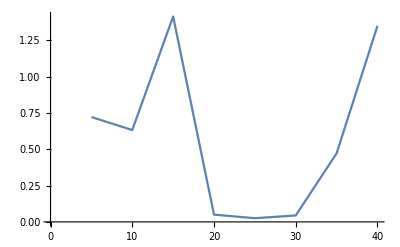

```mathematica
ListPlot[{{5,0.7220564998603923},{10,0.6325195509568072},{15,1.4145498624894974},{20,0.050057350740649625},{25,0.02542236731833495},{30,0.04430283576265956},{35,0.47187031136079943},{40,1.3498032807814695}},Joined->True]
```

```mathematica
Interpolation[{{5/10,0.20398638516148312},{10/10,0.1802478124451512},{15/10,0.39177568900809895/2.5},{20/10,4*0.02046411583307451},{25/10,2*0.0171983},{30/10,0.017020836280713797},{35/10,0.133643120997305},{40/10,0.3717489714145118}}]
```

InterpolatingFunction[…]

```mathematica
17.5*4
```

70.

```mathematica
Export["~/PhD/fig3_b_line.dat",Table[{50,y},{y,0,9,0.01}]]
```

~/PhD/fig3_b_line.dat

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["~/PhD/fig3_b_line.dat"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["~/PhD/fig3_b_line.dat"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["~/PhD/fig3_b.dat"]]]
```

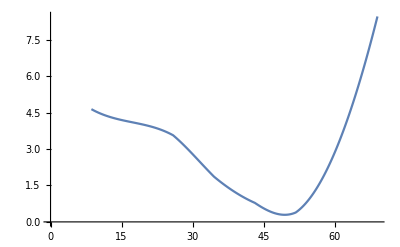

```mathematica
ListPlot[Table[{17.25x,22.75*%27[x]},{x,0.5,4.,0.01}],Joined->True]
```

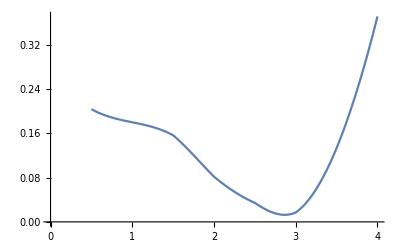

```mathematica
ListPlot[%30,Joined->True]
```

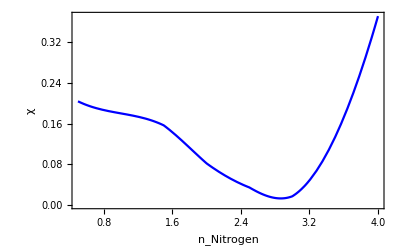

```mathematica
Plot[%139[x],{x,0.5,4.},Frame->True,PlotStyle->Blue,FrameLabel->{{HoldForm[χ],None},{HoldForm[Subscript[n, Nitrogen]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

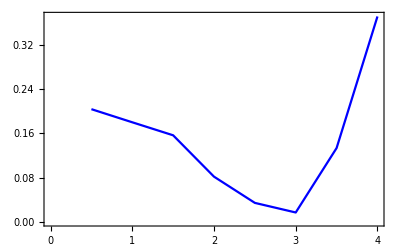

```mathematica
ListPlot[{{5/10,0.20398638516148312},{10/10,0.1802478124451512},{15/10,0.39177568900809895/2.5},{20/10,4*0.02046411583307451},{25/10,2*0.0171983},{30/10,0.017020836280713797},{35/10,0.133643120997305},{40/10,0.3717489714145118}},Joined->True,Frame->True,PlotStyle->Blue]
```

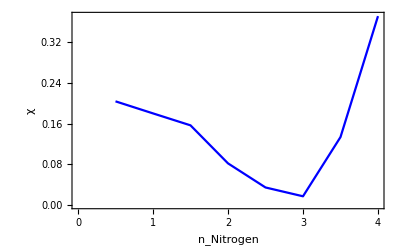

```mathematica
Show[%136,FrameLabel->{{HoldForm[χ],None},{HoldForm[Subscript[n, Nitrogen]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

```mathematica
Mean[Table[Table[fF1[1,a,y],{a,0,1.5,0.1}],{y,0.5,2.5,0.1}]]
```

Mean::rectt: Rectangular array expected at position 1 in Mean[{{{{{5,0.00731188},{10,0.0067357},{15,0.00652217},{20,0.00641181},{25,0.00556931},{30,0.00579593},{35,0.00506921},{40,0.0037097}},{{5,0.00693753},{10,0.00635029},{15,0.00608068},{20,0.00593711},{25,0.00509978},{30,0.00523091},{35,0.00451864},{40,0.00328815}},{{5,0.00674488},{10,0.00614672},{15,0.00586386},{20,0.00564131},{25,0.00484606},{30,0.00488745},{35,0.00419693},{40,0.00305292}},«45»,{{5,13.8844},{10,12.2384},{15,26.3397},{20,1.14918},{25,0.421903},{30,1.10614},{35,9.32307},{40,24.9849}},{{5,13.1906},{10,11.6269},{15,25.0231},{20,1.09214},{25,0.401229},{30,1.05124},{35,8.85734},{40,23.7361}},«30»},«14»,{«1»}},{«1»},«17»,{«1»},{«1»}}].

Mean[{1}]
 |  |  |  |

```mathematica
4.8390*10^17/(60*60*24*365)
```

1.53444×10^10

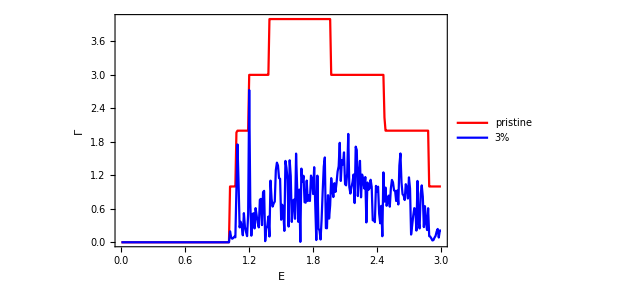

```mathematica
ListLinePlot[{Table[{ω,pris[ω,0.0001,1,1,-0.75,9]},{ω,Range[0,3,0.01]}],Table[{ω,device[ω,0.0001,1,0.5,9,212]},{ω,Range[0,3,0.01]}]},Frame->True,PlotStyle->{Red,Blue},FrameLabel->{{Γ,None},{Ε,None}},PlotLegends->Placed[{"pristine","3%"},{{0.2,0.8}}],LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]}]
```

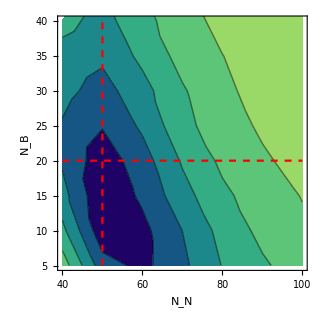
```mathematica
-Graphics--Graphics-
```